```mathematica
nf12[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
nf22[t_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
```

```mathematica
NIntegrate[nf1[y,-1],{y,0,0.9},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-2.904952786 ⅈ

```mathematica
NIntegrate[nf2[-1],{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

5.270055544 ⅈ

```mathematica
NIntegrate[nf1[y,-1],{y,0,0.9},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2[-1],{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.36510276 ⅈ

```mathematica
NIntegrate[nf12[y,-1],{y,0,0.8},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-2.904952947 ⅈ

```mathematica
Parallelize[lf1=Table[{y,inf1[y,-1]},{y,0,0.9,0.02}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
Parallelize[lg1=Table[{y,ing1[y,-1]},{y,0,0.9,0.005}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.37551083239751136388747819622023336357810126911467394763701×10^-14 ⅈ and 9.24299066431782744516814663762186481193073869736470345864969×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24182635926729297625302686352934676396790525367630759361023×10^-14 ⅈ and 7.4386697414878836534369648900855283093875390285374323006011×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.87022168182052498053517647341102448128452639209578128775367×10^-15 ⅈ and 3.2580082689206273007866299582320240690842800244626038694745×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.80410227018853676533930977425451225145006267819469634502284×10^-14 ⅈ and 5.83183017851264724968485583794273093871433146954271966766005×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -8.38039573470866876863450017692810017882488082124444646762831×10^-17 ⅈ and 2.91305095963703575702253625075617641838537169443601574663452×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -4.45698168297852018958102896608264945705243794343159501203035×10^-14 ⅈ and 4.94028840397738162500713574962226328843397416513169229505415×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.0140961181057085087644999936756553325490376497698360005254×10^-14 ⅈ and 1.80203859179933033925924603942809477245604847747698302145177×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

```mathematica
sf1=Interpolation[lf1];
```

```mathematica
sg1=Interpolation[lg1];
```

```mathematica
sg1[0.5]
```

0.+0.000212427 ⅈ

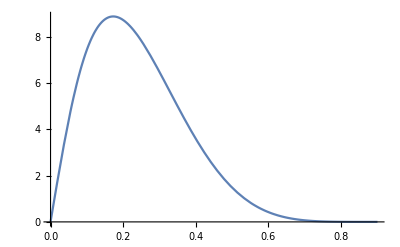

```mathematica
Plot[I*sf1[y],{y,0,0.9}]
```

```mathematica
path1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-f-xi1.pdf"}];
Export[path1,Labeled[Show[Plot[I*sf1[y],{y,0,1.1},PlotRange->{{0,0.9},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-f-xi1.pdf

```mathematica
NIntegrate[sf1[y,-1],{y,0,1.1}]+NIntegrate[nf2[-1],{k3,0,∞},{θ,0,2π},{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.+2.36511 ⅈ

```mathematica
NIntegrate[nf1[y,-1],{y,0,1.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2[-1],{k3,0,∞},{θ,0,2π},{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.36510276 ⅈ

```mathematica
nf12[y_,t_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
ng12[y_,t_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
nf22[t_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
ng22[t_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1}];
```

```mathematica
NIntegrate[nf12[y,-1],{y,0,1.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22[-1],{k3,0,∞},{θ,0,2π},{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.3651026 ⅈ

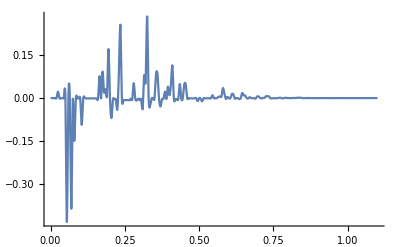

```mathematica
Plot[I*sg1[y],{y,0,1.1},PlotRange->All]
```

```mathematica
path=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"ed-g-xi1.pdf"}];
Export[path,Labeled[Show[Plot[(I)*sg1[x],{x,0,1.1},PlotRange->All],AxesStyle->Directive[Thick,16]],
{StyleBox["g",FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\ed-g-xi1.pdf

```mathematica
lg1
```

{{0.,0.000338975219 ⅈ},{0.005,0.00004956653703 ⅈ},{0.01,0.00006449904249 ⅈ},{0.015,0.0001490597138 ⅈ},{0.02,0.0001816951809 ⅈ},{0.025,-0.02280327498 ⅈ},{0.03,0.0002979947536 ⅈ},{0.035,0.0004019690842 ⅈ},{0.04,0.0004180644693 ⅈ},{0.045,0.0005098825811 ⅈ},{0.05,-0.009195967257 ⅈ},{0.055,0.4371616914 ⅈ},{0.06,0.0006317001714 ⅈ},{0.065,0.0007791095481 ⅈ},{0.07,0.3918001995 ⅈ},{0.075,0.0009241759092 ⅈ},{0.08,0.1516666881 ⅈ},{0.085,0.0008347333166 ⅈ},{0.09,0.001037494118 ⅈ},{0.095,0.001086546552 ⅈ},{0.1,0.001130063881 ⅈ},{0.105,0.0934347019 ⅈ},{0.11,0.001201298522 ⅈ},{0.115,-0.00114810075 ⅈ},{0.12,0.001253079478 ⅈ},{0.125,0.001272342525 ⅈ},{0.13,0.001287559449 ⅈ},{0.135,0.00101237761 ⅈ},{0.14,0.001016581424 ⅈ},{0.145,0.001018429998 ⅈ},{0.15,0.001018120689 ⅈ},{0.155,0.001015842569 ⅈ},{0.16,0.0018204333 ⅈ},{0.165,-0.07699516307 ⅈ},{0.17,0.001976117389 ⅈ},{0.175,-0.09345713442 ⅈ},{0.18,-0.01919246946 ⅈ},{0.185,-0.03175638012 ⅈ},{0.19,-0.005682891592 ⅈ},{0.195,-0.172027044 ⅈ},{0.2,0.002853065305 ⅈ},{0.205,0.06970044846 ⅈ},{0.21,0.004275844002 ⅈ},{0.215,0.004713015349 ⅈ},{0.22,0.005111078748 ⅈ},{0.225,0.04048994099 ⅈ},{0.23,-0.09014990281 ⅈ},{0.235,-0.2572629282 ⅈ},{0.24,0.001261919327 ⅈ},{0.245,0.006577634754 ⅈ},{0.25,0.006778961216 ⅈ},{0.255,0.006953632665 ⅈ},{0.26,0.007103252683 ⅈ},{0.265,0.007229358241 ⅈ},{0.27,0.002150059392 ⅈ},{0.275,0.004491410519 ⅈ},{0.28,-0.0529153221 ⅈ},{0.285,0.001738214568 ⅈ},{0.29,0.007643050431 ⅈ},{0.295,0.001655199176 ⅈ},{0.3,0.007697771786 ⅈ},{0.305,0.003271177844 ⅈ},{0.31,0.0388756269 ⅈ},{0.315,-0.08166693008 ⅈ},{0.32,-0.05343595616 ⅈ},{0.325,-0.2888722107 ⅈ},{0.33,0.0005646925592 ⅈ},{0.335,0.02515287601 ⅈ},{0.34,0.0009852152297 ⅈ},{0.345,0.0009570619762 ⅈ},{0.35,0.0009293597007 ⅈ},{0.355,-0.08438984145 ⅈ},{0.36,-0.08235725018 ⅈ},{0.365,0.002830952294 ⅈ},{0.37,0.02933166395 ⅈ},{0.375,0.003057486636 ⅈ},{0.38,0.003149548144 ⅈ},{0.385,-0.02289106925 ⅈ},{0.39,0.003295146135 ⅈ},{0.395,-0.04055598397 ⅈ},{0.4,-0.009421230329 ⅈ},{0.405,-0.04686757797 ⅈ},{0.41,-0.1143868256 ⅈ},{0.415,0.004132607299 ⅈ},{0.42,0.003474323434 ⅈ},{0.425,0.003473319288 ⅈ},{0.43,0.003465032788 ⅈ},{0.435,-0.05020492163 ⅈ},{0.44,0.00241101405 ⅈ},{0.445,0.0003273849317 ⅈ},{0.45,-0.04815924569 ⅈ},{0.455,-0.04676557784 ⅈ},{0.46,0.0004506380206 ⅈ},{0.465,0.0004751303909 ⅈ},{0.47,0.0006438180418 ⅈ},{0.475,0.001102549918 ⅈ},{0.48,0.001222645074 ⅈ},{0.485,0.0001811374885 ⅈ},{0.49,0.0001739124434 ⅈ},{0.495,0.01036619553 ⅈ},{0.5,0.0002124273012 ⅈ},{0.505,0.001854863461 ⅈ},{0.51,0.01154415841 ⅈ},{0.515,0.0001870873018 ⅈ},{0.52,0.0007431384015 ⅈ},{0.525,0.0007122269369 ⅈ},{0.53,0.0006822481644 ⅈ},{0.535,0.0003143664075 ⅈ},{0.54,0.0006250404681 ⅈ},{0.545,-0.0102587303 ⅈ},{0.55,0.0002734260357 ⅈ},{0.555,0.0001304713021 ⅈ},{0.56,0.0001244352615 ⅈ},{0.565,-0.004532474103 ⅈ},{0.57,-0.005436543943 ⅈ},{0.575,-0.005130634225 ⅈ},{0.58,-0.03520897641 ⅈ},{0.585,-0.01633006049 ⅈ},{0.59,0.003213208678 ⅈ},{0.595,-0.004038847847 ⅈ},{0.6,0.0003457588478 ⅈ},{0.605,0.000285780574 ⅈ},{0.61,-0.01376108439 ⅈ},{0.615,-0.01306607157 ⅈ},{0.62,0.001858486728 ⅈ},{0.625,0.000096042819 ⅈ},{0.63,0.0001210660939 ⅈ},{0.635,0.003357496336 ⅈ},{0.64,0.00004062405702 ⅈ},{0.645,-0.01811536452 ⅈ},{0.65,-0.009465696621 ⅈ},{0.655,-0.008997017393 ⅈ},{0.66,0.00006432239116 ⅈ},{0.665,0.0009627976454 ⅈ},{0.67,-0.003280829089 ⅈ},{0.675,0.00003577908816 ⅈ},{0.68,0.0002874675394 ⅈ},{0.685,0.00006314932135 ⅈ},{0.69,0.002002033924 ⅈ},{0.695,-0.005791834562 ⅈ},{0.7,-0.005462472896 ⅈ},{0.705,-0.0009581976818 ⅈ},{0.71,0.001295198054 ⅈ},{0.715,-0.0008130644973 ⅈ},{0.72,-0.0007475584954 ⅈ},{0.725,-0.006871371528 ⅈ},{0.73,-0.006425900709 ⅈ},{0.735,-0.006003280695 ⅈ},{0.74,0.0007199014869 ⅈ},{0.745,0.0006566859147 ⅈ},{0.75,0.0004066236482 ⅈ},{0.755,0.0004052959684 ⅈ},{0.76,0.0007768099501 ⅈ},{0.765,0.00003887493587 ⅈ},{0.77,-0.001051367394 ⅈ},{0.775,-0.0009122524211 ⅈ},{0.78,0.0009379643402 ⅈ},{0.785,0.0005657744848 ⅈ},{0.79,-0.001313143479 ⅈ},{0.795,-0.0003708275061 ⅈ},{0.8,-0.0002998023804 ⅈ},{0.805,2.457620177×10^-15 ⅈ},{0.81,-1.168465276×10^-14 ⅈ},{0.815,0.00004338321157 ⅈ},{0.82,-0.0008974063429 ⅈ},{0.825,0.0001233733771 ⅈ},{0.83,-0.001357588345 ⅈ},{0.835,-0.00123986881 ⅈ},{0.84,-0.001130628105 ⅈ},{0.845,-0.001029466082 ⅈ},{0.85,0.0004590313998 ⅈ},{0.855,0.0001726636116 ⅈ},{0.86,-0.0004695540479 ⅈ},{0.865,0.00001356908706 ⅈ},{0.87,-0.000386806992 ⅈ},{0.875,0.0001065803669 ⅈ},{0.88,0.00005448943931 ⅈ},{0.885,0.00007258007602 ⅈ},{0.89,0.00001064456101 ⅈ},{0.895,1.676353788×10^-6 ⅈ},{0.9,1.116093375×10^-6 ⅈ},{0.905,0.00005201454805 ⅈ},{0.91,-0.00006961350027 ⅈ},{0.915,0.00005194734903 ⅈ},{0.92,8.661267218×10^-6 ⅈ},{0.925,-0.0001141267625 ⅈ},{0.93,-0.0001005871522 ⅈ},{0.935,-2.221137932×10^-14 ⅈ},{0.94,0.0000248213184 ⅈ},{0.945,8.139146241×10^-6 ⅈ},{0.95,0.00002403276677 ⅈ},{0.955,0.00001543582246 ⅈ},{0.96,-1.800092364×10^-14 ⅈ},{0.965,-2.06738418×10^-14 ⅈ},{0.97,2.013870299×10^-6 ⅈ},{0.975,-0.00003788014081 ⅈ},{0.98,0.00001645005312 ⅈ},{0.985,-0.00002615582396 ⅈ},{0.99,3.011957294×10^-6 ⅈ},{0.995,2.491843154×10^-6 ⅈ},{1.,2.041838691×10^-6 ⅈ},{1.005,1.655593601×10^-6 ⅈ},{1.01,1.349145253×10^-6 ⅈ},{1.015,1.066436494×10^-6 ⅈ},{1.02,8.310054992×10^-7 ⅈ},{1.025,-2.677374144×10^-14 ⅈ},{1.03,8.222010527×10^-7 ⅈ},{1.035,-4.173465977×10^-7 ⅈ},{1.04,2.716191859×10^-7 ⅈ},{1.045,-1.241841397×10^-7 ⅈ},{1.05,1.68590485×10^-7 ⅈ},{1.055,-3.660775517×10^-14 ⅈ},{1.06,6.81782901×10^-8 ⅈ},{1.065,2.371497343×10^-8 ⅈ},{1.07,-1.208696526×10^-7 ⅈ},{1.075,-7.20987357×10^-15 ⅈ},{1.08,-1.370129739×10^-14 ⅈ},{1.085,-1.9350624×10^-14 ⅈ},{1.09,-2.423902578×10^-14 ⅈ},{1.095,-1.651825616×10^-14 ⅈ},{1.1,6.933156556×10^-15 ⅈ}}

```mathematica
sg1[0.1]
```

0.+0.00113006 ⅈ

```mathematica
nf1x1[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
nf1x2[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
nf1x3[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
```

```mathematica
inf1x1[y_]:=NIntegrate[nf1x1[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
inf1x2[y_]:=NIntegrate[nf1x2[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
inf1x3[y_]:=NIntegrate[nf1x3[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
lf1x1=ParallelTable[{y,inf1x1[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01]]}];
lf1x2=ParallelTable[{y,inf1x2[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001]]}];
lf1x3=ParallelTable[{y,inf1x3[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001],Range[0.9991,0.9999,0.0001]]}];
```

```mathematica
sf1x1=Interpolation[lf1x1];
sf1x2=Interpolation[lf1x2];
sf1x3=Interpolation[lf1x3];
```

```mathematica
path1x1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-f-xi01.pdf"}];
Export[path1x1,Labeled[Show[Plot[I*sf1x1[y],{y,0,0.99},PlotRange->{{0,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-f-xi01.pdf

```mathematica
path1x2=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-f-xi001.pdf"}];
Export[path1x2,Labeled[Show[Plot[I*sf1x2[y],{y,0,0.999},PlotRange->{{0,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-f-xi001.pdf

```mathematica
path1x3=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-f-xi0001.pdf"}];
Export[path1x3,Labeled[Show[Plot[I*sf1x1[y],{y,0,0.9999},PlotRange->{{0,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.0001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-f-xi0001.pdf

```mathematica
ing1hp[y_,t_]:=NIntegrate[ng1[y,t],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
Parallelize[lg1hp=Table[{y,ing1hp[y,-1]},{y,0,0.9,0.005}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
sg1hp=Interpolation[lg1hp];
```

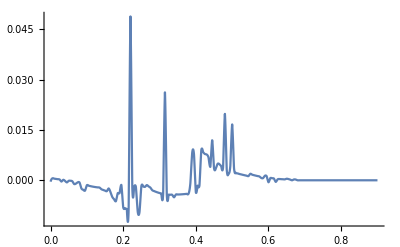

```mathematica
Plot[I*sg1hp[x],{x,0,0.9},PlotRange->All]
```

```mathematica
Parallelize[lg1mp=Table[{y,ing1[y,-1]},{y,0,0.9,0.001}]];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.37551083239751136388747819622023336357810126911467394763701×10^-14 ⅈ and 9.24299066431782744516814663762186481193073869736470345864969×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -9.84868512384570268392339042155171684060930812751265339512479×10^-15 ⅈ and 8.85287300920295800674751397727646957637757737026670621860793×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.328942049×10^-14 ⅈ and 1.070483913×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -3.44321787538022640134110656659422175116538992006168129305728×10^-14 ⅈ and 1.09406623651609156599169215551056374295844880830705554642019×10^-14 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.4049575880029741334522138482731547820499545494465839457758×10^-15 ⅈ and 1.05151369723665125976048247106480358580838834829772826897957×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.66301737534577154042601418355567065241487040782569821196722×10^-14 ⅈ and 5.89545252591918391482214562338841060744290218692289273715173×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.80410227018853676533930977425451225145006267819469634502284×10^-14 ⅈ and 5.83183017851264724968485583794273093871433146954271966766005×10^-16 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.35627998152029986040437150114839145039318773593190624293057×10^-14 ⅈ and 1.09627687186195167852882123312368285431446143361538343169086×10^-15 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.87022168182052498053517647341102448128452639209578128775367×10^-15 ⅈ and 3.2580082689206273007866299582320240690842800244626038694745×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.55062372978760370716029839935177828031215477695978930345408×10^-15 ⅈ and 5.52925633511276805744904418008452348973864192982329899169116×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.03325193666185738215868633992222413793594908536207423957599×10^-14 ⅈ and 3.11278816456541893721595589821846965470539718614228341043315×10^-17 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.768785505×10^-14 ⅈ and 3.018661398×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.24182635926729297625302686352934676396790525367630759361023×10^-14 ⅈ and 7.4386697414878836534369648900855283093875390285374323006011×10^-16 for the integral and error estimates.

```mathematica
sg1mp=Interpolation[lg1mp];
```

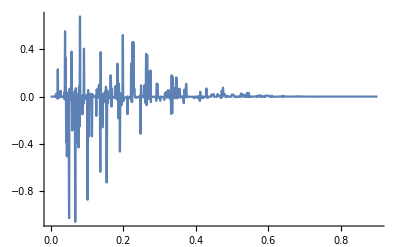

```mathematica
Plot[I*sg1mp[x],{x,0,0.9},PlotRange->All]
```

```mathematica
pathg=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-g-xi1.pdf"}];
Export[pathg,Labeled[Show[Plot[I*sg1[y],{y,0,0.9},PlotRange->{{0,1.1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-g-xi1.pdf

```mathematica
pathgmp=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-g-xi1-mp.pdf"}];
Export[pathgmp,Labeled[Show[Plot[I*sg1mp[y],{y,0,0.9},PlotRange->{{0,1.1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-g-xi1-mp.pdf

```mathematica
pathghp=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"d-g-xi1-hp.pdf"}];
Export[pathghp,Labeled[Show[Plot[I*sg1hp[y],{y,0,0.9},PlotRange->{{0,1.1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,"d"],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\d-g-xi1-hp.pdf